# Stochastic

```mathematica
Quit
```

```mathematica
nb1=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Common.nb"}]];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]
SetSelectedNotebook[EvaluationNotebook[]];
```

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
```

```mathematica
threshold=10^-3;

(*requires γ,delay*)
SEG[W_,noiseW_,zstart_,nIterations_]:=Module[{
V,noiseV,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff,
noisyHz,noisyHzbar,noisyHzdiff},
V[vec_]:=W@@vec;
noiseV[vec_]:=noiseW@@vec;
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
iterates[[n]]=zbar;
noisyHz=z-γ/Max[1,(n-delay)]*noiseV[z];
zbar=Q[noisyHz];
noisyHzbar=zbar-γ/Max[1,(n-delay)]*noiseV[zbar];
noisyHzdiff=noisyHzbar-noisyHz;

(*for plotting*)
Hz=z-γ/Max[1,(n-delay)]*V[z];
Hzbar=zbar-γ/Max[1,(n-delay)]*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;

z=z+(noisyHzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

(*requires γ and α,delay*)
SEGPlus[W_,noiseW_,zstart_,nIterations_]:=Module[{
V,noiseV,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff,
noisyHz,noisyHzbar,noisyHzdiff},
V[vec_]:=W@@vec;
noiseV[vec_]:=noiseW@@vec;
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
iterates[[n]]=zbar;
noisyHz=z-γ*noiseV[z];
zbar=Q[noisyHz];
noisyHzbar=zbar-γ*noiseV[zbar];
noisyHzdiff=noisyHzbar-noisyHz;

(*for plotting*)
Hz=z-γ*V[z];
Hzbar=zbar-γ*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;

z=z+α/Max[1,(n-delay)]*(noisyHzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

numTotalIterates=50;
plotIterates[W_,iterates_,legends_]:=Module[{},
Print[Length[iterates]];
iteratesReduces=Map[ArrayResample[#,numTotalIterates]&,iterates];
legend=If[Length[legends]≠0,ListLinePlot[iteratesReduces,
PlotMarkers->Automatic,
Joined->True,
PlotLegends->Placed[legends,Below]][[2]],{}];
lines=ListLinePlot[iterates,PlotLegends->legend];
markers=ListLinePlot[iteratesReduces,
PlotMarkers->Automatic,
Joined->False];
Show[
plotFlow[W,side],
lines,
markers,
Frame->True]];

(*requires init,T,noise*)
legends={};(*{"SEG","SEG+"}*)
plotAllStochasticMethods[W_]:=Module[{noiseW,norms,Hzdiffs},
noiseW[x_,y_]:=W[x,y]+noise* RandomVariate[NormalDistribution[],2];
SEGIterates=SEG[W,noiseW,init,T];
SEGPlusIterates=SEGPlus[W,noiseW,init,T];
iterates=Map[First,{SEGIterates,SEGPlusIterates}];
Hzdiffs=Map[Last,{SEGIterates,SEGPlusIterates}];
norms=Table[Table[Norm[p],{p,orbit}],{orbit,Hzdiffs}];
norms[[2]]=norms[[2]]*Table[1/γ,{t,1,Length[norms[[2]]]}];
norms[[1]]=norms[[1]]*Table[t/γ,{t,1,Length[norms[[1]]]}];
Print[
plotIterates[W,iterates,{"SEG","SEG+"}]];
ListLogLogPlot[norms,
Frame->True,
FrameLabel->{"k",MaTeX["\\frac{1}{\\gamma_k}\\|H\\bar{z}^k-Hz^k\\|"]},
Joined->True,
PlotLegends->Placed[legends,Below]]]
```

## Lower bound example

```mathematica
Clear[a,b];
c=1/3;
rule=Solve[b+(a c)/(√(1-c^2))==0,a][[1]][[1]]
```

a→-2 √2 b

2 √2

3

-1/9

{-x+2 √2 y,-2 √2 x-y}

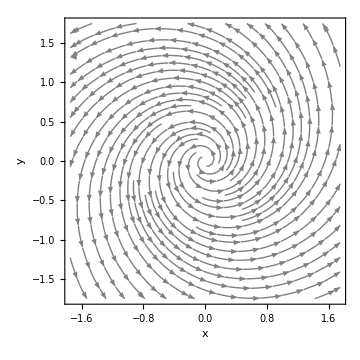

```mathematica
b=-1;
a=a/.rule
L=√(a^2+b^2)
ρ=b/(a^2+b^2)
F[x_,y_]:=a*x*y+b/2*x^2-b/2*y^2;
W[x_,y_]:=Evaluate@getW[F];
W[x,y]
plotFlow[W]
```

2

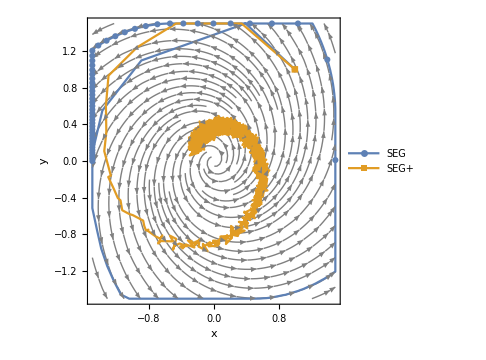

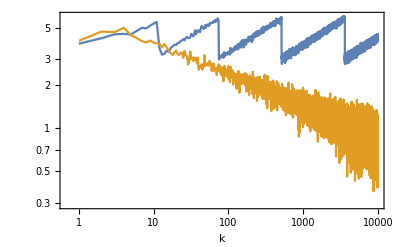

Figs/Stoc_Bilinear_invc=4.png

```mathematica
threshold=10^-7;
boundary=3/2;
side=3/2;
Q[z_]:=Clip[z,{-boundary,boundary}];
init={1.0,1.0};
noise=0.1;
delay=0;
T=10000;
γ=1/L;
α=1/2; (*first tracked iterate divides α by 2*)
plot=plotAllStochasticMethods[W]
Export["Figs/Stoc_Bilinear_invc=4.png",plot]
```

## GlobalForsaken

```mathematica
globalphi[z_]:=(z^2/3-z^4/3+z^6 2/21)
GlobalForsaken[x_,y_]:=x *y+globalphi[x]-globalphi[y]
W[x_,y_]:=Evaluate@getW[GlobalForsaken];
star={0,0};
weakMVIcondition[x_,y_]:=Evaluate@(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=Evaluate@Norm[J[x,y],2];
```

```mathematica
sides=4/3;
cons=-sides<=x<=sides&&-sides<=y<=sides;
L=Assuming[{x∈Reals,y∈Reals},MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify]
N[-1/(2L)]
```

(√(1/2 (74125591+9409 √59721901)))/2835

-0.165432

2

-Graphics-

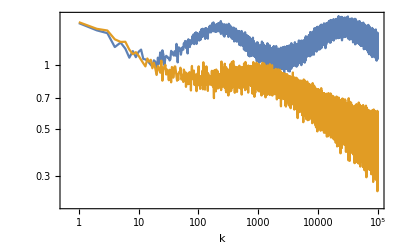

Figs/Stoc_GlobalForsaken.png

```mathematica
L=(√(1/2 (74125591+9409 √59721901)))/2835;
threshold=10^-7;
boundary=4/3;
side=4/3;
Q[z_]:=Clip[z,{-boundary,boundary}];
init={1.0,1.0};
noise=0.05;
delay=0;
T=100000;
γ=1/L;
α=0.6;(*first tracked iterate divides α by 2*)
plot=plotAllStochasticMethods[W]
Export["Figs/Stoc_GlobalForsaken.png",plot]
```